```mathematica
pts={{0,0,0},{1,1,1},{2,-1,1},{3,0,2},{0,2,0},{1,3,1},{2,-1,4},{3,0,2}};
```

```mathematica
Graphics3D[{BezierCurve[pts],Green,Line[pts],Red,Point[pts]}]
```

-Graphics3D-

```mathematica
data=Import[SystemDialogInput["FileOpen"]];
```

```mathematica
data
```

-Graphics-

```mathematica
ImageData[data]⟦1,200;;220⟧
```

{{1.,1.,1.,0.},{1.,1.,1.,0.},{1.,1.,1.,0.},{1.,1.,1.,0.},{1.,1.,1.,0.},{1.,1.,1.,0.},{1.,1.,1.,0.},{1.,1.,1.,0.},{1.,1.,1.,0.},{1.,1.,1.,0.},{0.52549,0.52549,0.52549,1.},{1.,1.,1.,0.},{1.,1.,1.,0.},{1.,1.,1.,0.},{1.,1.,1.,0.},{1.,1.,1.,0.},{1.,1.,1.,0.},{1.,1.,1.,0.},{1.,1.,1.,0.},{1.,1.,1.,0.},{1.,1.,1.,0.}}

```mathematica
IntegerDigits[{1,2,3},2,8]
```

{{0,0,0,0,0,0,0,1},{0,0,0,0,0,0,1,0},{0,0,0,0,0,0,1,1}}

```mathematica
FromDigits[%,MixedRadix[{2,2,2}]]
```

{0,0,0,0,0,0,3,5}

```mathematica
Fold[#1+#2&, 1-{1,0.8}]
```

0.2

```mathematica
dim = ImageDimensions[data]
pts={{{0,0},{0,300}}, {{0,0},{150,154}}};
graphics = Graphics[BezierCurve[pts],PlotRange->{{0,dim⟦1⟧},{0,dim⟦2⟧}}, ImageSize->dim]
array = Rasterize[graphics];
pixels = PixelValuePositions[array,Black, 0.5];
Fold[Plus,Map[Function[{x},Fold[#1+#2&, 1-PixelValue[data, x]⟦1;;3⟧]], pixels]]
```

{421,479}

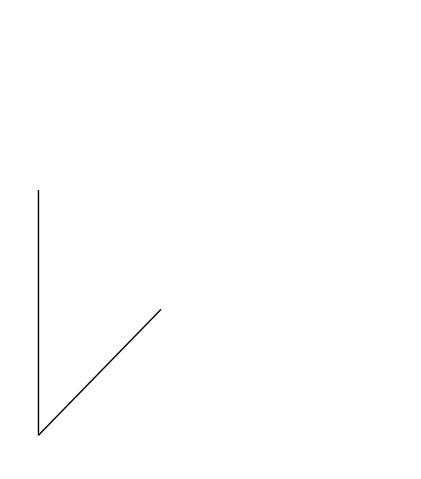

8.

```mathematica
ffit[img_, model_] := Fold[Plus,
Map[Function[{x},
Fold[#1+#2&,
 1-PixelValue[img, x]⟦1;;3⟧
]
], model]
]
```

```mathematica
BezierPhenotype[bin_, numCurves_, dimensions_, bezierOrder_, resolution_ ] := 
Module[
{frac, curvesFrac,curvesImSpace},
frac = Map[FromDigits[#,2]/(2^resolution)&,Partition[bin,resolution]];
curvesFrac = Partition[Partition[frac, dimensions], bezierOrder];
curvesImSpace = N[Map[Map[#*imgSpace&, #]&,curvesFrac]];
Return[curvesImSpace]
]
```

```mathematica
BinPopGenerator[numSamples_, strlength_] :=Table[Random[Integer, {0,1}], {i,1,numSamples}, {j,1,strlength}];
```

```mathematica
numGenoms  = 10;
numCurves = 20;
bezierOrder=3;
resolution = 10;
dimensions = 2;
imgSpace = ImageDimensions[data];

genotypes = BinPopGenerator [numGenoms,numCurves*dimensions*bezierOrder*resolution];

pts = Table[BezierPhenotype[genotypes⟦i⟧, numCurves, dimensions, bezierOrder, resolution], {i, 1,numGenoms}];
graphics = Table[Graphics[BezierCurve[pts⟦i⟧],PlotRange->{{0,imgSpace⟦1⟧},{0,imgSpace⟦2⟧}}, ImageSize->imgSpace], {i, 1,numGenoms}];
array = Table[Rasterize[graphics⟦i⟧], {i, 1,numGenoms}];
pixels = Table[PixelValuePositions[array⟦i⟧,Black, 0.5], {i, 1,numGenoms}];
```

{{365,472},{365,471},{364,470},{363,469},{363,468},{362,467},{362,466},{361,465},{360,464},{361,464},{360,463},{359,462},{336,461},{359,461},{336,460},{358,460},{335,459},{358,459},{335,458},{357,458},{334,457},{356,457},{99,456},{334,456},{356,456},{99,455},{333,455},{355,455},6081,{374,37},{375,37},{376,37},{108,36},{269,36},{107,35},{269,35},{107,34},{269,34},{106,33},{269,33},{106,32},{269,32},{105,31},{269,31},{105,30},{269,30},{269,29},{269,28},{269,27},{269,26},{269,25},{269,24},{269,23},{269,22},{269,21},{269,20},{269,19}}
 |  |  |  |

```mathematica
ffit[data, pixels⟦1⟧]
```

486.506

```mathematica
RandomReal[1,{10,20}]
```

{{0.171533,0.249371,0.809683,0.699396,0.424681,0.517309,0.955528,0.364315,0.407784,0.840854,0.498495,0.801513,0.257267,0.191415,0.130192,0.32418,0.462073,0.684328,0.982556,0.28249},{0.915819,0.381334,0.259318,0.670387,0.314797,0.927854,0.418224,0.108324,0.985693,0.948693,0.947969,0.23896,0.377282,0.866308,0.945711,0.710923,0.218094,0.516472,0.710457,0.481675},{0.191092,0.586406,0.061533,0.794556,0.907271,0.197245,0.191033,0.988071,0.439043,0.486124,0.47385,0.341382,0.0460587,0.0738953,0.406448,0.538985,0.0454193,0.809693,0.681992,0.684782},{0.0590075,0.439146,0.0825485,0.184745,0.545921,0.471839,0.648606,0.627092,0.555337,0.526301,0.0118126,0.371294,0.487972,0.597779,0.762138,0.204916,0.675755,0.142716,0.426294,0.820414},{0.725326,0.196825,0.0288821,0.774871,0.580132,0.956128,0.961248,0.640513,0.167734,0.691128,0.283034,0.481158,0.427318,0.203528,0.563439,0.206955,0.62279,0.811998,0.442141,0.892891},{0.114714,0.0689008,0.0521764,0.87338,0.134336,0.257824,0.514809,0.145169,0.0787778,0.41287,0.450613,0.0841637,0.531637,0.844365,0.467502,0.475202,0.874908,0.523938,0.071914,0.589477},{0.412867,0.935227,0.510979,0.486951,0.527455,0.028368,0.13879,0.559924,0.455252,0.0228743,0.595238,0.336495,0.204389,0.852144,0.0514518,0.528011,0.649148,0.48872,0.494715,0.285595},{0.704239,0.567349,0.180628,0.464087,0.512771,0.388335,0.982787,0.802441,0.815932,0.966184,0.079632,0.384034,0.331741,0.648609,0.118851,0.172328,0.608119,0.345734,0.595671,0.178975},{0.408964,0.103613,0.204891,0.7867,0.617978,0.329043,0.400883,0.192477,0.988921,0.0165655,0.994888,0.514302,0.488103,0.338145,0.488804,0.9247,0.368439,0.684744,0.589299,0.298227},{0.568557,0.280146,0.98885,0.715755,0.576201,0.100402,0.55894,0.425199,0.305639,0.0391143,0.956973,0.903259,0.413031,0.475254,0.468167,0.633629,0.388586,0.177422,0.211533,0.0914465}}

```mathematica
match = SparseArray[Map[#->Fold[#1+#2&,
 1-PixelValue[data, #]⟦1;;3⟧
]&,pixels⟦1⟧]]
```

PixelValue::imginv: Expecting an image or graphics instead of data.

Part::take: Cannot take positions 1 through 3 in PixelValue[data,{114,464}].

PixelValue::imginv: Expecting an image or graphics instead of data.

Part::take: Cannot take positions 1 through 3 in PixelValue[data,{114,464}].

PixelValue::imginv: Expecting an image or graphics instead of data.

General::stop: Further output of PixelValue::imginv will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 3 in PixelValue[data,{113,463}].

General::stop: Further output of Part::take will be suppressed during this calculation.

SparseArray[<5741>, {407, 464}]

```mathematica
ArrayPlot[match]
```

-Graphics-